# 3基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.908446969051692×10^9

#### 変数

```mathematica
date="20230920"
```

20230920

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/IODATA/NII/togo-log/rcoslogs/"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/

```mathematica
(*basedir=mountdir<>"log/D="<>date<>"/T=4"*)
```

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20230920.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20230920.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

16260867 217713283 7711269280 log-20230920.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=ci.P~5

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

3147791

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{3147791,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.90416×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-09-19T15:00:00Z
log.ci0001.aws.wa01.yobi
126.119.36.67
host":"-
user":"-
3.90416×10^9
method":"GET
https://cir.nii.ac.jp/
code":"200
size":"10420
https://www.clib.kindai.ac.jp/
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.0.0 Safari/537.36
http_x_forwarded_for":"\"126.119.36.67\"
request_time":"0.045
upstream_response_time":"0.045"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

StringTake::take: Cannot take positions 1 through 19 in "res".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-09-19T15:00:00Z
log.ci0001.aws.wa01.yobi
52.233.106.132
host":"-
user":"-
3.90416×10^9
method":"GET
https://cir.nii.ac.jp/crid/1520290883665556096
code":"200
size":"14300
-
agent":"Mozilla/5.0 AppleWebKit/537.36 (KHTML, like Gecko; compatible; GPTBot/1.0; +https://openai.com/gptbot)
http_x_forwarded_for":"\"52.233.106.132\"
request_time":"0.020
upstream_response_time":"0.021"}
1520290883665556096
toCRID[-]

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=cs.R=.P=

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

24628

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{24628,14}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{24628,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"/user/chang-j@openidp.nii.ac.jp/qxka3-osfstorage-72xtwbbh/rstudio/events/get_events

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2023-09-20T00:00:00.230770331+09:00

```mathematica
logdateToTime["cs"][strSplt1CC["cs"][[1]][[6]]]
```

3.90416×10^9

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2023-09-19T15:01:21Z
log.cs0002.ksw.wa01.yobi
106.73.34.97
stream":"stdout
user":"-
3.90416×10^9
date_time":"19/Sep/2023:15:01:20 +0000
https://jupyter.cs.rcos.nii.ac.jp/user/chang-j@openidp.nii.ac.jp/qxka3-osfstorage-72xtwbbh/rstudio/events/get_events
method":"POST
code":"200
https://jupyter.cs.rcos.nii.ac.jp/user/chang-j@openidp.nii.ac.jp/qxka3-osfstorage-72xtwbbh/rstudio/
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10.15; rv:109.0) Gecko/20100101 Firefox/114.0
size":"150
hostname":"fluentd-bllnp"}

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=la.T~ea.A~hc.A~go.A~bot.P~api

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

85013

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{85013,12}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{{log.la0001.aws.wa01.yobi,84998},{log.la0003.aws.wa01.yobi,3},{log.la0002.aws.wa01.yobi,12}}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{84998,12}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{12,12}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{3,12}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

2023-09-19T15:00:02Z
log.la0001.aws.wa01.yobi
{"user":"f5cd5ad93a8da7216b02105a706e8e5fa67925e09917d2d7311044245181c68d
date_time":"20/Sep/2023:00:00:02 +0900
method":"GET
path":"/pluginfile.php/73135/mod_scorm/content/2/text/audio/02_03/08_ja.mp3
code":"206
size":"2
referer":"https://lms.nii.ac.jp/pluginfile.php/73135/mod_scorm/content/2/text/02_03.html
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Safari/605.1.15
http_x_forwarded_for":"153.246.209.241
session_id":"9m1us83resq82tlq8qus1uf0d8"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{84998,12}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

2023-09-20T09:38:07Z
log.la0002.aws.wa01.yobi
{"user":"-
date_time":"20/Sep/2023:09:38:07 +0000
method":"GET
path":"/
code":"302
size":"242
referer":"-
agent":"Mozilla/5.0 (Macintosh; U; Intel Mac OS X 10_6_4; en-US) AppleWebKit/534.1 (KHTML, like Gecko) Chrome/104.0.0.0 Safari/534.1
http_x_forwarded_for":"34.229.89.23
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{12,12}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

2023-09-19T15:14:54Z
log.la0003.aws.wa01.yobi
{"user":"-
date_time":"19/Sep/2023:15:14:54 +0000
method":"GET
path":"/
code":"302
size":"-
referer":"-
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/111.0.0.0 Safari/537.36
http_x_forwarded_for":"103.171.163.225
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{3,12}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{85013,12}

```mathematica
strSplt1R["la"][[1]]
```

{2023-09-19T15:00:02Z,log.la0001.aws.wa01.yobi,http_x_forwarded_for":"153.246.209.241,size":"2,method":"GET,date_time":"20/Sep/2023:00:00:02 +0900,code":"206,path":"/pluginfile.php/73135/mod_scorm/content/2/text/audio/02_03/08_ja.mp3,{"user":"f5cd5ad93a8da7216b02105a706e8e5fa67925e09917d2d7311044245181c68d,session_id":"9m1us83resq82tlq8qus1uf0d8"},referer":"https://lms.nii.ac.jp/pluginfile.php/73135/mod_scorm/content/2/text/02_03.html,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Safari/605.1.15}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.90416×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2023-09-19T15:00:02Z
log.la0001.aws.wa01.yobi
http_x_forwarded_for":"153.246.209.241
size":"2
method":"GET
3.90419×10^9
code":"206
https://lms.nii.ac.jp/pluginfile.php/73135/mod_scorm/content/2/text/audio/02_03/08_ja.mp3
{"user":"f5cd5ad93a8da7216b02105a706e8e5fa67925e09917d2d7311044245181c68d
session_id":"9m1us83resq82tlq8qus1uf0d8"}
https://lms.nii.ac.jp/pluginfile.php/73135/mod_scorm/content/2/text/02_03.html
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Safari/605.1.15

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{85013,12}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

2023-09-19T15:00:02Z
log.la0001.aws.wa01.yobi
153.246.209.241
size":"2
method":"GET
3.90419×10^9
code":"206
https://lms.nii.ac.jp/pluginfile.php/73135/mod_scorm/content/2/text/audio/02_03/08_ja.mp3
{"user":"f5cd5ad93a8da7216b02105a706e8e5fa67925e09917d2d7311044245181c68d
session_id":"9m1us83resq82tlq8qus1uf0d8"}
https://lms.nii.ac.jp/pluginfile.php/73135/mod_scorm/content/2/text/02_03.html
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Safari/605.1.15

### データ(wk)

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=wk.P~4.A~bot

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

531

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{531}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{531,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ことなる形式ログを落とす。

```mathematica
(strSplt1CCC["wk","pre"]=Cases[strSplt1CC["wk"],x_/;StringTake[x[[6]],9]=="date_time"])//Dimensions
```

{521,12}

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2023-09-19T15:02:13+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.90416×10^9

```mathematica
(strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CCC["wk","pre"]])//Dimensions
```

{521,12}

ソースアドレスを値だけにする。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2023-09-19T18:49:25Z
log.wk1001.oci.wa01.yobi
185.16.39.117
user":"-
method":"GET
3.90417×10^9
code":"200
https://jdcat.jsps.go.jp/oai?verb=GetRecord&metadataPrefix=ddi&identifier=oai:jdcat.jsps.go.jp:00013678
size":"6411
http_x_forwarded_for":"185.16.39.117"}
-
agent":"Mozilla/5.0 (X11; Linux x86_64; rv:103.0) Gecko/20100101 Firefox/103.0

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{36.7826,{3257953}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{3257953}

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{37.7263,{3147791,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-09-20T00:17:47Z
log.ci0001.aws.wa02.yobi
100.0.47.202
host":"-
user":"-
3.90419×10^9
method":"GET
https://cir.nii.ac.jp/crid/1130282268633535232
code":"200
size":"12716
https://scholar.google.com/scholar_lookup?title=The+history+of+cardiac+surgery,+1896-1955&author=SL+Johnson&publication_year=1970&
agent":"Mozilla/5.0 (iPhone; CPU iPhone OS 16_6_1 like Mac OS X) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Mobile/15E148 Safari/604.1
http_x_forwarded_for":"\"100.0.47.202\"
request_time":"0.098
upstream_response_time":"0.100"}
1130282268633535232
toCRID[https://scholar.google.com/scholar_lookup?title=The+history+of+cardiac+surgery,+1896-1955&author=SL+Johnson&publication_year=1970&]
1

### ckanデータの処理

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{3257953}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

221

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

221

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{3257953}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

13

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

13

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

234

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

234

ciデータからのCKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{3147791}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690857923906708608,1690576448930482048,1690013498975829760,1690857923900834048,1690013498965926272,1690576448922801792,1690294973943937792,1690857977695145728,1690857923906471552,1690013498980458112,1690857923896586240,1690576448934320256,1690013498971634176,1690294973950045184,1690013498971530752,1690857923901692928,1690857923901692928,1690013498975987456,1690576448922270080,1690013498968840576,1690013498969646464,1690013498969646464,1690857923908999552,1690857923906655744,1690013552764922368,1690013498970822400,1690294973948129280,1690295027741508864,1690295027741508864,1690857977694930304,1690294973948129280,1690294973958133120,1690013498970606464,1690857923898919680,1690857923898518912,1690013498966791040,1690013498976675840,1690576448931825536,1690576448934520192,1690576448931117184,1690294973952905216,1690013498966657152,1690294973946098048,1690857923900066816,1690294973945918464,1690294973954822144,1690013498974911744,1690857923906980992,1690294973950413312,1690857977695057024,1690576448918251264,1690576448918363904,1690576448919106944,1690857923906123136,1690013498976638592,1690294973952645120,1690576448929908608,1690013498967846784,1690013498981199104,1690857923902214144,1690857923902214144,1690295027741353216,1690576448923739520,1690576448923739520,1690576448934416512,1690013498976522496,1690013498980589312,1690294973952144512,1690013498968803968,1690576448930314112,1690013498967202176,1690857923910469632,1690294973943246720,1690294973943752960,1690294973944228864,1690857923906123136,1690294973947560960,1690013498975318272,1690294973953252608,1690576448925375104,1690294973941684352,1690013498966659712,1690576448918772864,1690013498969479424,1690576448928900352,1690857923895650176,1690576448930310272,1690857923895650176,1690294973943125888,1690013498970167808,1690294973953740160,1690576524385069696,1690294973943427456,1690013498970595456,1690857923904243328,1690294973956950272,1690857923901246464,1690294973943660544,1690294973955174272,1690857923899432832,1690294973949860864,1690294973942126592,1690294973954759040,1690857923904420992,1690857923904420992,1690294973943125888,1690013498969328768,1690013498974193024,1690294973943635968,1690576448933878144,1690294973953347840,1690294973951558400,1690857923904420992,1690857923899432832,1690857923906980992,1690294973947672064,1690013498972144384,1690294973946457728,1690013498975265280,1690013498979864192,1690013498970167040,1690013498969104384,1690013498979146496,1690013498980703104,1690013498980439168,1690294973953551488,1690294973943507072,1690013498976848384,1690013498978861184,1690013498976106624,1690857923902564224,1690013498964675968,1690013498964576896,1690013498964675968,1690857923900185856,1690576448931792768,1690013498968695040,1690013498977412480,1690857923898541568,1690013498968272640,1690576448925002496,1690294973944016512,1690576448919662336,1690013498980276992,1690013498980082816,1690857923903726464,1690013498970469632,1690013498980777600,1690857923903869440,1690857923910288256,1690294973946036352,1690857923900935552,1690857923900128768,1690576448923698816,1690857923910651776,1690013498965386368,1690857923907275008,1690576448931736320,1690576448934284160,1690294973941856768,1690857923898876672,1690576448932432256,1690857923896100608,1690576448930919168,1690857923901353728,1690013498977788416,1690294973957600768,1690013498972105600,1690857923898002944,1690013498966025600,1690857923910841984,1690857923897504896,1690576448923585536,1690576448924865152,1690294973952681728,1690013498968010880,1690294973943916800,1690857923900755456,1690294973954008064,1690857923907275776,1690294973958363136,1690294973942232704,1690857923901818752,1690013498965383424,1690013498971263232,1690013498977690368,1690576448918805888,1690294973944213248,1690576448930647680,1690857923901454976,1690576448934654336,1690576448935010944,1690576448921202816,1690294973957821568,1690576448924059648,1690857923901326080,1690294973955842688,1690294973957879680,1690294973947678208,1690013498965770112,1690013498972067072,1690857923896008576,1690857923901402368,1690294973956647040,1690294973957481728,1690576448926258944,1690294973944642688,1690294973954550272,1690857923907794048,1690857923897655680,1690294973954675968,1690576448922190464,1690576448929367680,1690294973949723264,1690294973945873536,1690013498976125696,1690857923902332672,1690013498977396864,1690294973948139648,1690857923911237504,1690857923900866688}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690857923906471552,1690013498971530752,1690857923906655744,1690857923906655744,1690295027741508864,1690013498976638592,1690294973952144512,1690294973941684352,1690294973941684352,1690294973941684352,1690013498976848384,1690013498976848384,1690013498964675968}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964576896,1690013498964675968,1690013498965383424,1690013498965386368,1690013498965770112,1690013498965926272,1690013498966025600,1690013498966657152,1690013498966659712,1690013498966791040,1690013498967202176,1690013498967846784,1690013498968010880,1690013498968272640,1690013498968695040,1690013498968803968,1690013498968840576,1690013498969104384,1690013498969328768,1690013498969479424,1690013498969646464,1690013498970167040,1690013498970167808,1690013498970469632,1690013498970595456,1690013498970606464,1690013498970822400,1690013498971263232,1690013498971530752,1690013498971634176,1690013498972067072,1690013498972105600,1690013498972144384,1690013498974193024,1690013498974911744,1690013498975265280,1690013498975318272,1690013498975829760,1690013498975987456,1690013498976106624,1690013498976125696,1690013498976522496,1690013498976638592,1690013498976675840,1690013498976848384,1690013498977396864,1690013498977412480,1690013498977690368,1690013498977788416,1690013498978861184,1690013498979146496,1690013498979864192,1690013498980082816,1690013498980276992,1690013498980439168,1690013498980458112,1690013498980589312,1690013498980703104,1690013498980777600,1690013498981199104,1690013552764922368,1690294973941684352,1690294973941856768,1690294973942126592,1690294973942232704,1690294973943125888,1690294973943246720,1690294973943427456,1690294973943507072,1690294973943635968,1690294973943660544,1690294973943752960,1690294973943916800,1690294973943937792,1690294973944016512,1690294973944213248,1690294973944228864,1690294973944642688,1690294973945873536,1690294973945918464,1690294973946036352,1690294973946098048,1690294973946457728,1690294973947560960,1690294973947672064,1690294973947678208,1690294973948129280,1690294973948139648,1690294973949723264,1690294973949860864,1690294973950045184,1690294973950413312,1690294973951558400,1690294973952144512,1690294973952645120,1690294973952681728,1690294973952905216,1690294973953252608,1690294973953347840,1690294973953551488,1690294973953740160,1690294973954008064,1690294973954550272,1690294973954675968,1690294973954759040,1690294973954822144,1690294973955174272,1690294973955842688,1690294973956647040,1690294973956950272,1690294973957481728,1690294973957600768,1690294973957821568,1690294973957879680,1690294973958133120,1690294973958363136,1690295027741353216,1690295027741508864,1690576448918251264,1690576448918363904,1690576448918772864,1690576448918805888,1690576448919106944,1690576448919662336,1690576448921202816,1690576448922190464,1690576448922270080,1690576448922801792,1690576448923585536,1690576448923698816,1690576448923739520,1690576448924059648,1690576448924865152,1690576448925002496,1690576448925375104,1690576448926258944,1690576448928900352,1690576448929367680,1690576448929908608,1690576448930310272,1690576448930314112,1690576448930482048,1690576448930647680,1690576448930919168,1690576448931117184,1690576448931736320,1690576448931792768,1690576448931825536,1690576448932432256,1690576448933878144,1690576448934284160,1690576448934320256,1690576448934416512,1690576448934520192,1690576448934654336,1690576448935010944,1690576524385069696,1690857923895650176,1690857923896008576,1690857923896100608,1690857923896586240,1690857923897504896,1690857923897655680,1690857923898002944,1690857923898518912,1690857923898541568,1690857923898876672,1690857923898919680,1690857923899432832,1690857923900066816,1690857923900128768,1690857923900185856,1690857923900755456,1690857923900834048,1690857923900866688,1690857923900935552,1690857923901246464,1690857923901326080,1690857923901353728,1690857923901402368,1690857923901454976,1690857923901692928,1690857923901818752,1690857923902214144,1690857923902332672,1690857923902564224,1690857923903726464,1690857923903869440,1690857923904243328,1690857923904420992,1690857923906123136,1690857923906471552,1690857923906655744,1690857923906708608,1690857923906980992,1690857923907275008,1690857923907275776,1690857923907794048,1690857923908999552,1690857923910288256,1690857923910469632,1690857923910651776,1690857923910841984,1690857923911237504,1690857977694930304,1690857977695057024,1690857977695145728}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964576896→True,1690013498964675968→True,1690013498965383424→True,1690013498965386368→True,1690013498965770112→True,1690013498965926272→True,1690013498966025600→True,1690013498966657152→True,1690013498966659712→True,1690013498966791040→True,1690013498967202176→True,1690013498967846784→True,1690013498968010880→True,1690013498968272640→True,1690013498968695040→True,1690013498968803968→True,1690013498968840576→True,1690013498969104384→True,1690013498969328768→True,1690013498969479424→True,1690013498969646464→True,1690013498970167040→True,1690013498970167808→True,1690013498970469632→True,1690013498970595456→True,1690013498970606464→True,1690013498970822400→True,1690013498971263232→True,1690013498971530752→True,1690013498971634176→True,1690013498972067072→True,1690013498972105600→True,1690013498972144384→True,1690013498974193024→True,1690013498974911744→True,1690013498975265280→True,1690013498975318272→True,1690013498975829760→True,1690013498975987456→True,1690013498976106624→True,1690013498976125696→True,1690013498976522496→True,1690013498976638592→True,1690013498976675840→True,1690013498976848384→True,1690013498977396864→True,1690013498977412480→True,1690013498977690368→True,1690013498977788416→True,1690013498978861184→True,1690013498979146496→True,1690013498979864192→True,1690013498980082816→True,1690013498980276992→True,1690013498980439168→True,1690013498980458112→True,1690013498980589312→True,1690013498980703104→True,1690013498980777600→True,1690013498981199104→True,1690013552764922368→True,1690294973941684352→True,1690294973941856768→True,1690294973942126592→True,1690294973942232704→True,1690294973943125888→True,1690294973943246720→True,1690294973943427456→True,1690294973943507072→True,1690294973943635968→True,1690294973943660544→True,1690294973943752960→True,1690294973943916800→True,1690294973943937792→True,1690294973944016512→True,1690294973944213248→True,1690294973944228864→True,1690294973944642688→True,1690294973945873536→True,1690294973945918464→True,1690294973946036352→True,1690294973946098048→True,1690294973946457728→True,1690294973947560960→True,1690294973947672064→True,1690294973947678208→True,1690294973948129280→True,1690294973948139648→True,1690294973949723264→True,1690294973949860864→True,1690294973950045184→True,1690294973950413312→True,1690294973951558400→True,1690294973952144512→True,1690294973952645120→True,1690294973952681728→True,1690294973952905216→True,1690294973953252608→True,1690294973953347840→True,1690294973953551488→True,1690294973953740160→True,1690294973954008064→True,1690294973954550272→True,1690294973954675968→True,1690294973954759040→True,1690294973954822144→True,1690294973955174272→True,1690294973955842688→True,1690294973956647040→True,1690294973956950272→True,1690294973957481728→True,1690294973957600768→True,1690294973957821568→True,1690294973957879680→True,1690294973958133120→True,1690294973958363136→True,1690295027741353216→True,1690295027741508864→True,1690576448918251264→True,1690576448918363904→True,1690576448918772864→True,1690576448918805888→True,1690576448919106944→True,1690576448919662336→True,1690576448921202816→True,1690576448922190464→True,1690576448922270080→True,1690576448922801792→True,1690576448923585536→True,1690576448923698816→True,1690576448923739520→True,1690576448924059648→True,1690576448924865152→True,1690576448925002496→True,1690576448925375104→True,1690576448926258944→True,1690576448928900352→True,1690576448929367680→True,1690576448929908608→True,1690576448930310272→True,1690576448930314112→True,1690576448930482048→True,1690576448930647680→True,1690576448930919168→True,1690576448931117184→True,1690576448931736320→True,1690576448931792768→True,1690576448931825536→True,1690576448932432256→True,1690576448933878144→True,1690576448934284160→True,1690576448934320256→True,1690576448934416512→True,1690576448934520192→True,1690576448934654336→True,1690576448935010944→True,1690576524385069696→True,1690857923895650176→True,1690857923896008576→True,1690857923896100608→True,1690857923896586240→True,1690857923897504896→True,1690857923897655680→True,1690857923898002944→True,1690857923898518912→True,1690857923898541568→True,1690857923898876672→True,1690857923898919680→True,1690857923899432832→True,1690857923900066816→True,1690857923900128768→True,1690857923900185856→True,1690857923900755456→True,1690857923900834048→True,1690857923900866688→True,1690857923900935552→True,1690857923901246464→True,1690857923901326080→True,1690857923901353728→True,1690857923901402368→True,1690857923901454976→True,1690857923901692928→True,1690857923901818752→True,1690857923902214144→True,1690857923902332672→True,1690857923902564224→True,1690857923903726464→True,1690857923903869440→True,1690857923904243328→True,1690857923904420992→True,1690857923906123136→True,1690857923906471552→True,1690857923906655744→True,1690857923906708608→True,1690857923906980992→True,1690857923907275008→True,1690857923907275776→True,1690857923907794048→True,1690857923908999552→True,1690857923910288256→True,1690857923910469632→True,1690857923910651776→True,1690857923910841984→True,1690857923911237504→True,1690857977694930304→True,1690857977695057024→True,1690857977695145728→True|>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

152627

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{6.1948,{152627,1}}

```mathematica
idxLogS[4][[1]]
```

{{2023-09-20T00:17:47Z,log.ci0001.aws.wa02.yobi,100.0.47.202,host":"-,user":"-,3.90419×10^9,method":"GET,https://cir.nii.ac.jp/crid/1130282268633535232,code":"200,size":"12716,https://scholar.google.com/scholar_lookup?title=The+history+of+cardiac+surgery,+1896-1955&author=SL+Johnson&publication_year=1970&,agent":"Mozilla/5.0 (iPhone; CPU iPhone OS 16_6_1 like Mac OS X) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/16.6 Mobile/15E148 Safari/604.1,http_x_forwarded_for":"\"100.0.47.202\",request_time":"0.098,upstream_response_time":"0.100"},1130282268633535232,toCRID[https://scholar.google.com/scholar_lookup?title=The+history+of+cardiac+surgery,+1896-1955&author=SL+Johnson&publication_year=1970&],1}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

/Volumes/elecom/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.009851,Null}

#### Pre Op 2.2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
userGrER[4][[2]]
```

{{https://scholar.google.com/https://cir.nii.ac.jp/crid/1360292620871028736{3.90417×10^9,2}}}

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

152627

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}];
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions]
```

{180.795,{152627,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[4]=Map[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ]
```

{207.9,{152627,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{152627,3}

```mathematica
storyGrIdxFl[4][[1]][[3]][[1]]//EdgeList
```

{https://scholar.google.com/scholar_lookup?title=The+history+of+cardiac+surgery,+1896-1955&author=SL+Johnson&publication_year=1970&https://cir.nii.ac.jp/crid/1130282268633535232{3.90419×10^9,1}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{226287,3}

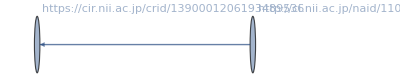
{20230920,{15,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{226287,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll=.
```

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

{226287,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{204133,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{174349,3}

上が分離されたストーリー

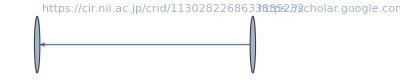
{20230920,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs3[4][[1]]
```

#### Pre Op 2.2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
Directory[]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
(*Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]*)
```

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

## Analysis

#### Analysis 1

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{174349}

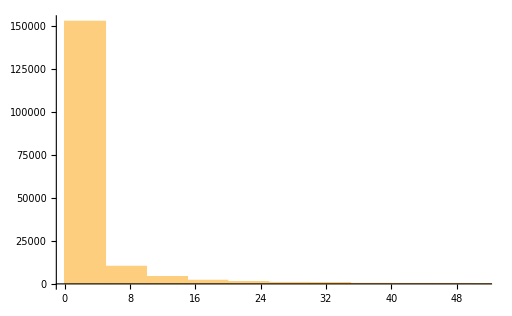

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{174349}

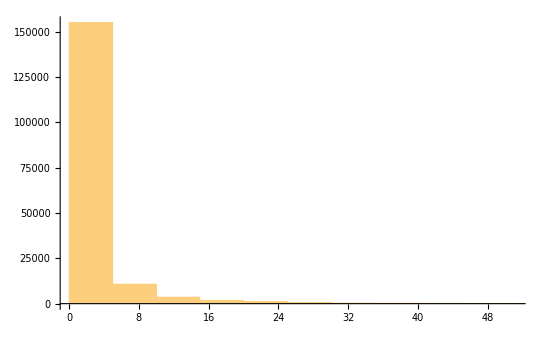

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{174349}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{174349}

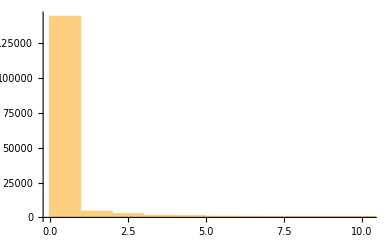

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{174349}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{174349}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{174349}

#### Analysis 2

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{174349}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{39,40,46,187,202,231,232,235,269,271,304,331,332,378,379,416,423,572,654,662,745,752,783,785,786,996,997,1028,1354}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:dsr.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:cir.nii.ac.jp,https:doshisha.repo.nii.ac.jp,https:ds.gakunin.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:lms.nii.ac.jp,https:nrid.nii.ac.jp,https:office.gakunin.nii.ac.jp,https:openidp.nii.ac.jp,https:otsuma.repo.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:redmine.devops.rcos.nii.ac.jp,https:support.irdb.nii.ac.jp,https:support.nii.ac.jp,https:toyo.repo.nii.ac.jp,https:www.nii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*\\.nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*\\.jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{174349}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,159395},{1,14950},{3,4}}

```mathematica
(GrBasesTly[4]=Tally[ GrBases[4]])//Dimensions
```

{1573,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,113620},{2,60661},{0,68}}

```mathematica
(GrNiiBasesTly[4]= Tally[GrNiiBases[4]])//Dimensions
```

{35,2}

```mathematica
TableForm[GrNiiBasesTly[4]]
```

https:cir.nii.ac.jp | 112928
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 24688
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 35145
https:lms.nii.ac.jp | 609
https:ds.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 16
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 9
https:jupyter.cs.rcos.nii.ac.jp | 82
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 136
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 4
 | 68
https:cir.nii.ac.jp
https:support.nii.ac.jp | 92
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 3
https:cir.nii.ac.jp
https:www.nii.ac.jp | 6
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 329
https:cir.nii.ac.jp
https:nrid.nii.ac.jp | 195
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 7
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 5
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:cir.nii.ac.jp
https:office.gakunin.nii.ac.jp | 2
https:cir.nii.ac.jp
https:toyo.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:otsuma.repo.nii.ac.jp | 1
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 1
https:redmine.devops.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 2
https:cir.nii.ac.jp
https:doshisha.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:support.irdb.nii.ac.jp | 1
http:dsr.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

#### Analysis 3 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{174349}

```mathematica
ckanGrP[4][[2]]
```

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{174349}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{174349}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{79,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{13,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{80,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{80,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{28,2,5,2,11,2,2,3,4,2,11,11,6,5,13,6,23,5,19,9,12,46,23,5,11,38,36,33,78,85,79,13,11,2,44,37,37,9,4,6,20,19,3,24,17,14,7,2,282,294,283,283,34,8,83,85,83,83,83,53,67,81,80,4,32,2,2,45,24,22,23,2,29,2,10,14,2,6,2,36}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{15270.,0.,65.,0.,10046.,0.,0.,5.,100.,0.,8259.,8197.,160.,85.,161.,5483.,34780.,8134.,1311.,611.,428.,7589.,1035.,110.,4473.,1858.,1833.,1080.,17190.,22589.,17180.,809.,1562.,0.,24163.,24163.,24163.,13825.,593.,1461.,2308.,2163.,11.,26428.,11187.,2256.,327.,0.,24190.,36703.,24190.,24190.,30078.,41639.,27334.,27327.,27327.,27327.,27327.,13449.,24755.,3036.,3006.,165.,24972.,0.,0.,640.,21768.,21364.,21364.,0.,27577.,0.,196.,225.,0.,196.,0.,29591.}

#### Analysis 4 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{80,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1582,1},{2630,1},{4033,1},{7218,1},{11954,1},{12855,1},{13250,1},{17687,1},{18075,1},{18456,1},{21851,1},{21851,1},{23265,1},{24605,1},{25891,1},{30251,1},{33733,1},{34989,1},{39200,1},{47383,1},{50683,1},{50975,1},{54675,1},{56091,1},{56419,1},{57734,1},{57734,1},{58352,1},{59762,1},{59762,1},{59762,1},{61185,1},{64737,1},{66206,1},{68858,1},{68858,1},{68858,1},{69200,1},{70069,1},{70072,1},{70085,1},{70085,1},{70085,1},{70287,1},{70287,1},{70287,1},{73453,1},{80381,1},{85869,1},{85869,1},{85869,1},{85869,1},{86652,1},{86652,1},{86701,1},{86701,1},{86701,1},{86701,1},{86701,1},{87037,1},{87037,1},{87202,1},{87202,1},{88530,1},{91386,1},{91473,1},{94925,1},{94987,1},{95450,1},{95450,1},{95450,1},{95892,1},{99273,1},{99804,1},{101757,1},{137786,1},{139273,1},{142307,1},{143592,1},{144328,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{28,2,5,2,11,2,2,3,4,2,11,11,6,5,13,6,23,5,19,9,12,46,23,5,11,38,36,33,78,85,79,13,11,2,44,37,37,9,4,6,20,19,3,24,17,14,7,2,282,294,283,283,34,8,83,85,83,83,83,53,67,81,80,4,32,2,2,45,24,22,23,2,29,2,10,14,2,6,2,36}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{62,1,5,1,18,1,1,3,4,1,19,19,8,5,16,5,31,5,36,12,19,85,24,6,17,65,63,46,124,135,113,21,17,1,49,44,44,9,3,8,30,26,2,35,26,20,10,1,436,457,438,454,4,7,138,144,137,133,136,68,90,164,154,3,56,1,1,132,70,56,57,1,44,1,19,17,1,7,1,33}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{80}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{244.15,0,0.733333,0,139.133,0,0,0.0666667,1.53333,0,134.517,134.517,0.866667,0.616667,0.683333,90.9167,557.45,71.1667,15.45,6.71667,2.7,65.1833,6.43333,0.7,53.6333,8.66667,8.66667,1.28333,51.8667,82.6333,57.1333,4.38333,12.8833,0,139.433,139.433,139.433,83.8833,9.8,23.5667,7.13333,7.13333,0.183333,326.65,148.5,35.1667,3.21667,0,62.1,60.8,62.1,62.1,494.117,413.,113.717,67.8833,113.717,113.717,113.717,174.7,173.65,6.7,8.58333,1.43333,207.233,0,0,0.933333,137.633,168.933,168.933,0,274.367,0,0.816667,0.766667,0,1.3,0,256.217}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{15270.,0.,65.,0.,10046.,0.,0.,5.,100.,0.,8259.,8197.,160.,85.,161.,5483.,34780.,8134.,1311.,611.,428.,7589.,1035.,110.,4473.,1858.,1833.,1080.,17190.,22589.,17180.,809.,1562.,0.,24163.,24163.,24163.,13825.,593.,1461.,2308.,2163.,11.,26428.,11187.,2256.,327.,0.,24190.,36703.,24190.,24190.,30078.,41639.,27334.,27327.,27327.,27327.,27327.,13449.,24755.,3036.,3006.,165.,24972.,0.,0.,640.,21768.,21364.,21364.,0.,27577.,0.,196.,225.,0.,196.,0.,29591.}

```mathematica
staytimeCKAN/60
```

{254.5,0.,1.08333,0.,167.433,0.,0.,0.0833333,1.66667,0.,137.65,136.617,2.66667,1.41667,2.68333,91.3833,579.667,135.567,21.85,10.1833,7.13333,126.483,17.25,1.83333,74.55,30.9667,30.55,18.,286.5,376.483,286.333,13.4833,26.0333,0.,402.717,402.717,402.717,230.417,9.88333,24.35,38.4667,36.05,0.183333,440.467,186.45,37.6,5.45,0.,403.167,611.717,403.167,403.167,501.3,693.983,455.567,455.45,455.45,455.45,455.45,224.15,412.583,50.6,50.1,2.75,416.2,0.,0.,10.6667,362.8,356.067,356.067,0.,459.617,0.,3.26667,3.75,0.,3.26667,0.,493.183}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://search.yahoo.co.jp/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{80}

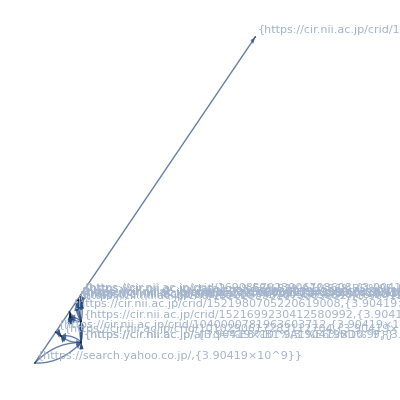
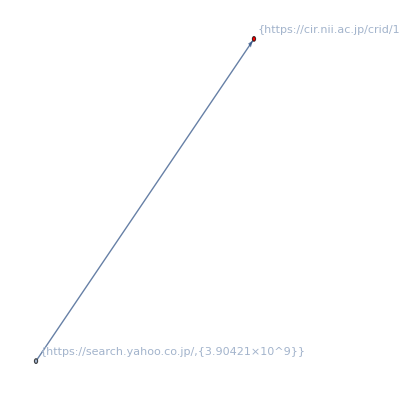
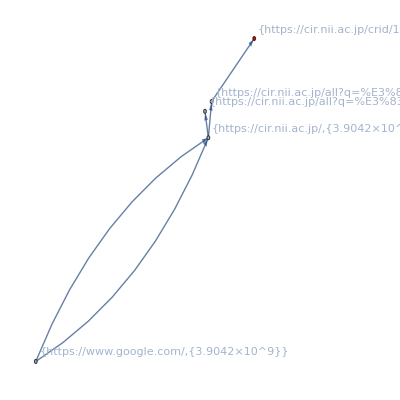
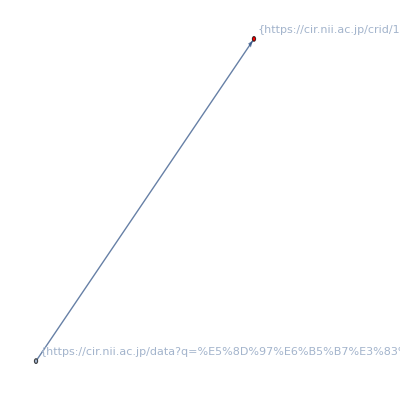
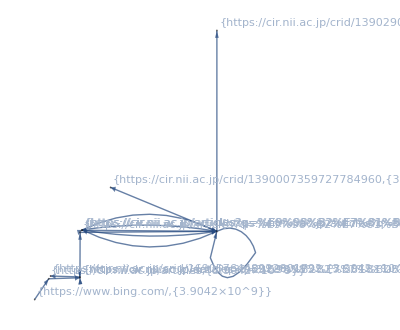
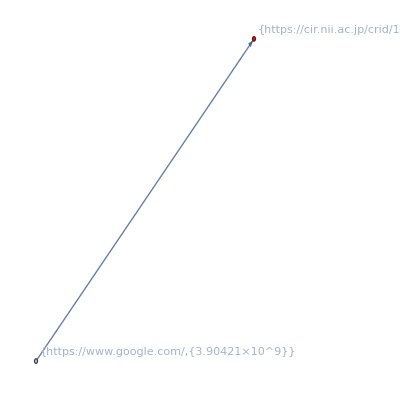
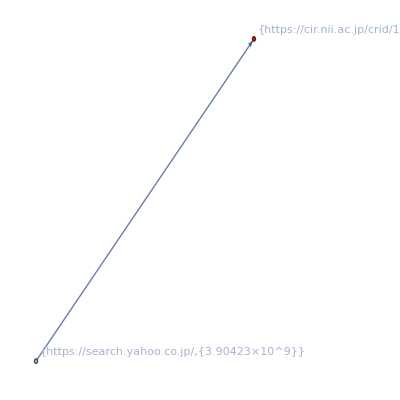
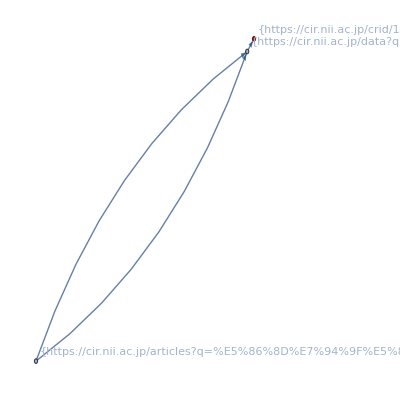
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ckanGrPRselHLTL[4]//TableForm
```

#### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[4]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 16260867
3257953

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 221
13
234 | 207
9
207

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 174349
80

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80 | 1582 | 1
2630 | 1
4033 | 1
7218 | 1
11954 | 1
12855 | 1
13250 | 1
17687 | 1
18075 | 1
18456 | 1
21851 | 1
21851 | 1
23265 | 1
24605 | 1
25891 | 1
30251 | 1
33733 | 1
34989 | 1
39200 | 1
47383 | 1
50683 | 1
50975 | 1
54675 | 1
56091 | 1
56419 | 1
57734 | 1
57734 | 1
58352 | 1
59762 | 1
59762 | 1
59762 | 1
61185 | 1
64737 | 1
66206 | 1
68858 | 1
68858 | 1
68858 | 1
69200 | 1
70069 | 1
70072 | 1
70085 | 1
70085 | 1
70085 | 1
70287 | 1
70287 | 1
70287 | 1
73453 | 1
80381 | 1
85869 | 1
85869 | 1
85869 | 1
85869 | 1
86652 | 1
86652 | 1
86701 | 1
86701 | 1
86701 | 1
86701 | 1
86701 | 1
87037 | 1
87037 | 1
87202 | 1
87202 | 1
88530 | 1
91386 | 1
91473 | 1
94925 | 1
94987 | 1
95450 | 1
95450 | 1
95450 | 1
95892 | 1
99273 | 1
99804 | 1
101757 | 1
137786 | 1
139273 | 1
142307 | 1
143592 | 1
144328 | 1 | 28
2
5
2
11
2
2
3
4
2
11
11
6
5
13
6
23
5
19
9
12
46
23
5
11
38
36
33
78
85
79
13
11
2
44
37
37
9
4
6
20
19
3
24
17
14
7
2
282
294
283
283
34
8
83
85
83
83
83
53
67
81
80
4
32
2
2
45
24
22
23
2
29
2
10
14
2
6
2
36 | 62
1
5
1
18
1
1
3
4
1
19
19
8
5
16
5
31
5
36
12
19
85
24
6
17
65
63
46
124
135
113
21
17
1
49
44
44
9
3
8
30
26
2
35
26
20
10
1
436
457
438
454
4
7
138
144
137
133
136
68
90
164
154
3
56
1
1
132
70
56
57
1
44
1
19
17
1
7
1
33 | 244.15
0
0.733333
0
139.133
0
0
0.0666667
1.53333
0
134.517
134.517
0.866667
0.616667
0.683333
90.9167
557.45
71.1667
15.45
6.71667
2.7
65.1833
6.43333
0.7
53.6333
8.66667
8.66667
1.28333
51.8667
82.6333
57.1333
4.38333
12.8833
0
139.433
139.433
139.433
83.8833
9.8
23.5667
7.13333
7.13333
0.183333
326.65
148.5
35.1667
3.21667
0
62.1
60.8
62.1
62.1
494.117
413.
113.717
67.8833
113.717
113.717
113.717
174.7
173.65
6.7
8.58333
1.43333
207.233
0
0
0.933333
137.633
168.933
168.933
0
274.367
0
0.816667
0.766667
0
1.3
0
256.217 | 254.5
0.
1.08333
0.
167.433
0.
0.
0.0833333
1.66667
0.
137.65
136.617
2.66667
1.41667
2.68333
91.3833
579.667
135.567
21.85
10.1833
7.13333
126.483
17.25
1.83333
74.55
30.9667
30.55
18.
286.5
376.483
286.333
13.4833
26.0333
0.
402.717
402.717
402.717
230.417
9.88333
24.35
38.4667
36.05
0.183333
440.467
186.45
37.6
5.45
0.
403.167
611.717
403.167
403.167
501.3
693.983
455.567
455.45
455.45
455.45
455.45
224.15
412.583
50.6
50.1
2.75
416.2
0.
0.
10.6667
362.8
356.067
356.067
0.
459.617
0.
3.26667
3.75
0.
3.26667
0.
493.183

### Export:CKAN impact

エクスポート用：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{80}

```mathematica
(ckanELX=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}])//Dimensions
```

{80}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230920/T=4/_story

```mathematica
(*Export["ckanedgelist.json",ckanELX]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.908019979365585×10^9

```mathematica
end-start
```

955.635785